```mathematica
(*grades, anonymized, post-first stage processing*)
grades={{4,3,2,4,5,2,3,2,1,26},{4,3,2,4,6,2,4,2,1,28},{0,2,1,1,0,0,0,0,1,5},{3,2,2,3,5,0,1,2,1,19},{2,3,1,4,5,0,0,2,0,17},{4,3,2,4,6,2,3,2,1,27},{4,2,2,4,5,2,3,2,2,26},{4,1,1,4,4,0,0,2,0,16},{3,1,1,1,5,0,0,1,1,13},{4,3,2,4,5,1,4,3,2,28},{4,3,2,2,6,0,0,2,1,20},{4,3,2,3,3,1,0,2,2,20},{4,3,1,4,5,1,0,2,0,20},{4,3,2,4,5,2,3,2,1,26},{4,3,2,4,5,2,3,2,1,26},{4,2,1,3,4,0,0,2,1,17},{4,3,2,3,5,0,2,2,1,22},{3,2,2,3,5,1,0,2,2,20},{4,3,2,4,5,1,1,2,2,24},{4,3,2,4,6,1,1,2,2,25},{4,3,2,4,6,2,4,2,2,29},{4,3,2,1,5,1,0,2,1,19},{4,2,1,1,6,2,1,2,1,20},{4,1,1,3,1,0,0,1,0,11},{3,2,2,4,5,0,2,3,0,21},{2,2,2,3,4,0,0,3,1,17},{4,2,2,4,5,0,2,3,0,22},{4,3,2,4,6,2,4,3,2,30},{4,2,2,4,4,1,0,2,0,19}};
scores=Transpose[grades];
```

```mathematica
(*compute correlation matrix*)
corr=ConstantArray[0,{Length[scores],Length[scores]}];
For[i=1,i≤Length[scores],i++,
For[j=1,j≤Length[scores],j++,
corr[[i]][[j]]=N[Correlation[scores[[i]],scores[[j]]]];
]
]
```

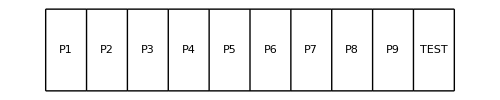
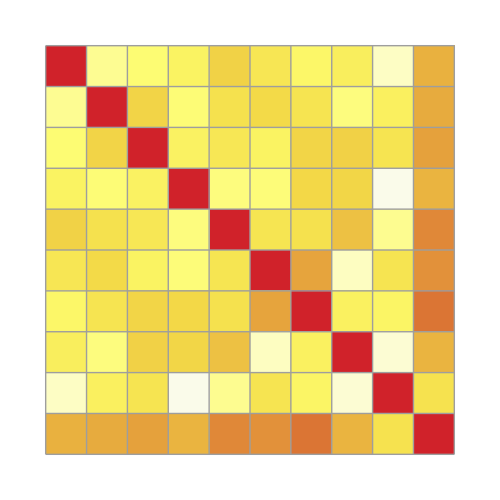
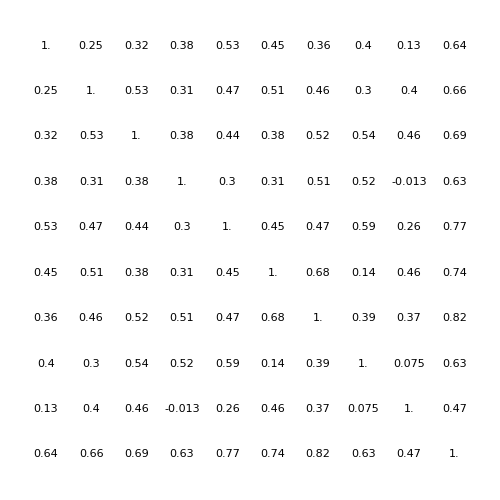
-Graphics-
-Graphics--Graphics--Graphics-

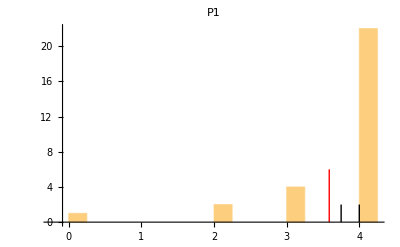
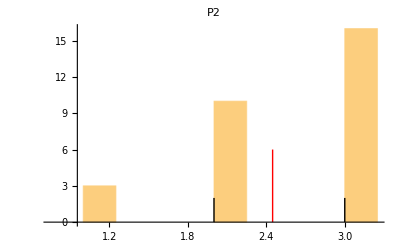
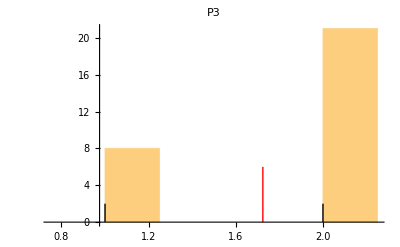
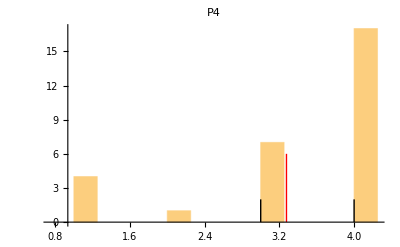
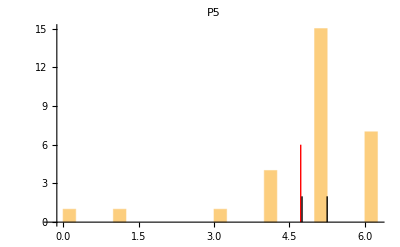
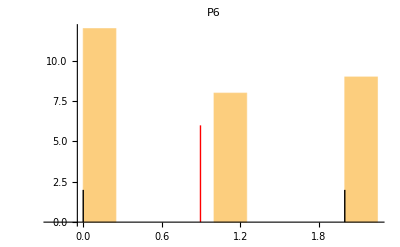
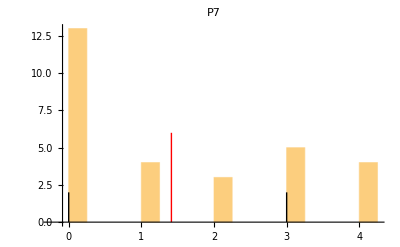
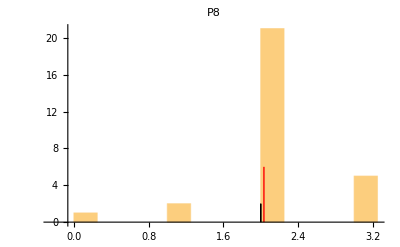

-Graphics-

```mathematica
(*labels for the correlation array*)
labels={P1,P2,P3,P4,P5,P6,P7,P8,P9,TEST};
(*Fancy picture*)
Column[{GraphicsRow[labels,ImageSize->500,Frame->All],Row[{GraphicsColumn[labels,ImageSize->50,Frame->All],Overlay[{ArrayPlot[corr,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->500,ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,corr,{2}],ImageSize->500]}]}]},Alignment->Right,Spacings->0]
(*histograms,for,each,problem,&,test,as,a,whole*)
histograms={};
For[i=1,i≤Length[scores],i++,
histograms=Append[histograms,Histogram[scores[[i]],{.25},Epilog->{Directive[{Thick,Red}],Line[{{Mean[scores[[i]]],0},{Mean[scores[[i]]],6}}],{Directive[{Thick,Black}],Line[{{Quartiles[scores[[i]]][[1]],0},{Quartiles[scores[[i]]][[1]],2}}],Line[{{Quartiles[scores[[i]]][[3]],0},{Quartiles[scores[[i]]][[3]],2}}]}},PlotLabel->labels[[i]]]];
]
histograms
histograms[[Length[histograms]]]
```

```mathematica
Export["test.png",histograms[[10]]]
```

test.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["p1.png"]]]
```